## Guide to the differential equations course package “diffEqClass`”

To load the package:

```mathematica
Needs["diffEqClass`"]
```

### The diffEq class object

setupDiffEq

setup[problem, options] sets up an ODE problem as a diffEq[] object.  The ODE problem may be a general ODE, an IVP, or a BVP.

diffEq [under construction]

diffEq[...] is an object representing an ODE problem and implements various methods of solving, using and analyzing the ODE.

### Commands

portrait1D

portrait1D[ode, {x, x1, x2},{t, t1, t2}] plots phase portrait/solutions for first-order ode in terms of x’(t), x(t)

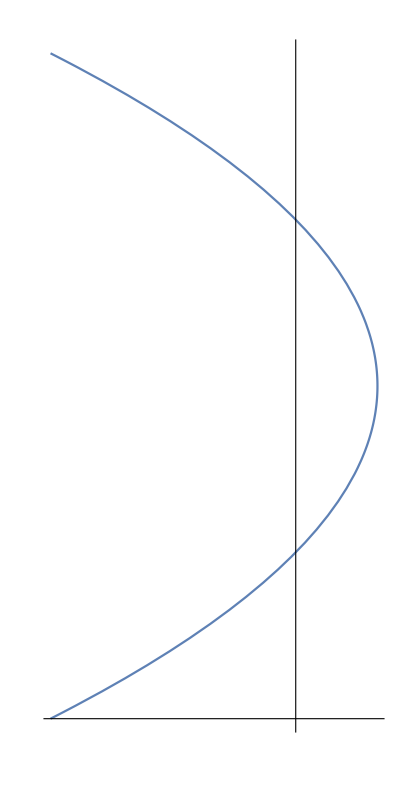
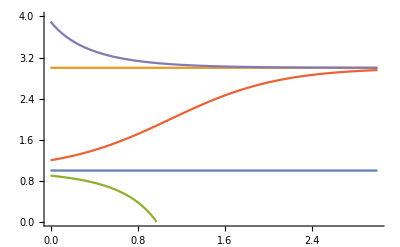
x'(t)==(1-x(t)) (x(t)-3) |  | 
-Graphics- | -Graphics- | -Graphics-
x vs. v | vector field | x vs. t

```mathematica
portrait1D[x'[t]==(1-x[t])(x[t]-3),{x,0,4},{t,0,3}]
```

polarPortrait1D

polarPortrait1D[ode, {r, r1, r2}, {t, t1, t2}] plots integral curves of direction field for an autonomous first-order ode in polar coordinates

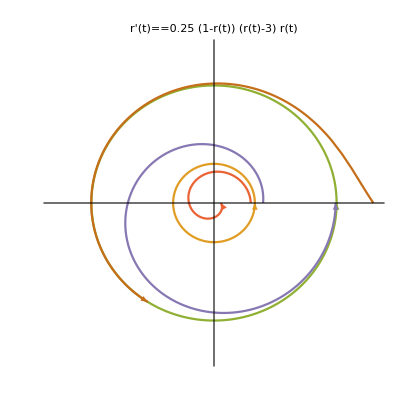

```mathematica
polarPortrait1D[r'[t]==0.25r[t](1-r[t])(r[t]-3),{r,0,4},{t,0,2Pi}]
```

### Tutorials

Phase Space

Poincaré Map

### Examples

Damped Harmonic Oscillator

Pendulum

### Explorations

These demonstrations call up a notebook with a manipulable app that allows you to explore some concept in differential equations.

```mathematica
diffEqDemo[] (* lists names of all available apps and classes of apps *)
```

{equilibrium,lyapunov,lyapunov3d,stability}

```mathematica
diffEqDemo["stability"] (* lists the apps concerning stability of critical points *)
```

{equilibrium,lyapunov,lyapunov3d}

```mathematica
diffEqDemo["equilibrium"] (* calls up the app for exploring the notion of stability of critical points *)
```